# Unit 11 - Sequences, Series, Fixed Point, CobwebPlot, and Finite Difference Formulas

Sequences

Recursive sequences and cobweb plots

The fixed-point iteration method for solving nonlinear equations

Series

Taylor series

Taylor series and finite difference formulas

## Sequences

A sequence is a list in Mathematica. Therefore, it is not new to us. We can use Table, Range, Dopaclet:ref/DoNonepaclet:ref/Do, For, While, NestList, or some other built-in functions to generation a sequence.

ListPlot can be used to plot a sequence. It is a powerful tool for plotting data with a number of options. Its basic usages are as follows.

ListPlot[{y_1,y_2,…}], plotting points (1,y_1), (2,y_2), ⋯, corresponding to a sequence {y_1,y_2,⋯}.

ListPlot[{list_1,list_2,…}], plotting multiple lists of points.

ListPlot[{{x_1,y_1},{x_2,y_2},…}], plotting a list of points with specified x and y coordinates.

Example 1
Generate and plot the first 30 terms of the sequence a_n=n^2/(n^2+1),n=1,2,3,⋯.

```mathematica
seq=Table[n^2/(n^2+1),{n,1,30}]
```

{1/2,4/5,9/10,16/17,25/26,36/37,49/50,64/65,81/82,100/101,121/122,144/145,169/170,196/197,225/226,256/257,289/290,324/325,361/362,400/401,441/442,484/485,529/530,576/577,625/626,676/677,729/730,784/785,841/842,900/901}

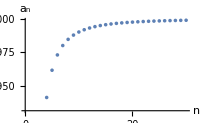

```mathematica
ListPlot[seq,AxesLabel->{n,Subscript[a, n]},ImageSize->200]
```

We can add a horizontal line for the limiting value of a_n as n approaches infinity, using the following function, ListPlotWithLimits.

Usage:
                      seq: The sequence to be represented on the real number line
{x,xMin,xMax}:  They are actually n, the minimum and maximum values of the index of the sequence {a_n}.
{y,yMin,yMax}:  They actually defines the PlotRange. To show the dashed lines for the limits, yMin and yMax should be a little bit smaller and larger, respectively.
                  limits:  A list of “limits” as n→∞. For example, for a_n=(-1)^n n/(n+1), limits={-1,1} when n is odd and even, respectively.

```mathematica
ListPlotWithLimits[seq_,{x_,xMin_,xMax_},{y_,yMin_,yMax_},limits_]:=
Show[{
ListPlot[seq,PlotRange->{yMin,yMax},PlotStyle->{Red,PointSize[Medium]},AxesLabel->{n,Subscript[a, n]},ImageSize->250],
Table[Plot[limits[[i]],{x,xMin,xMax},PlotStyle->Dashed],{i,Length[limits]}]
}];
```

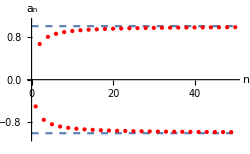

```mathematica
Clear[n]
ListPlotWithLimits[Table[(-1)^n n/(n+1),{n,50}],{x,0,50},{y,-1.1,1.1},{-1,1}]
```

We may also plot terms of a sequence on a real number line according to their values, using the function, SequenceLinearPlot, defined below.

Usage:
                      seq: The sequence to be represented on the real number line
{x,xMin,xMax}:  They are actually the possible minimum and maximum values of a_n.
                indices:  A list of indices of selected markers a_i to be printed on the graph. Not necessary to be 1, 2, 3, ⋯.
      markersYPos:  The y-coordinate of markers on the graph
   markersHeight:  The height of little vertical “ticks” representing a term of the sequence on the number line.
      graphHeight:  The y-coordinate corresponding to the height of the graph.
        plotOptions:  Plot options such as Ticks→{{0,0.5,1},{}}

```mathematica
Clear[a]
SequenceLinearPlot[seq_,{x_,xMin_,xMax_},indices_,markersYPos_,markersHeight_,graphHeight_,plotOptions___]:=
Module[{marker},
marker[i_]:=Subscript[a,indices[[i]]];
Show[{
Plot[graphHeight,{x,xMin,xMax},PlotRange->{-.02,graphHeight+0.01},Axes->{True,False},AspectRatio->Automatic,PlotStyle->White,plotOptions],
Graphics[{Red,PointSize[Medium],Table[Point[{seq[[indices[[i]]]],0}],{i,Length[indices]}]}],
Table[Graphics[Text[marker[i],{seq[[indices[[i]]]],markersYPos}]],{i, Length[indices]}],
Table[Graphics[{Red,Thin,Line[{{seq[[i]],0},{seq[[i]],markersHeight}}]}],{i,1,Length[indices]}],
Table[Graphics[{Red,Thin,Line[{{seq[[i]],0},{seq[[i]],3markersHeight/4}}]}],{i,Length[indices],Length[seq]}]
},ImageSize->350]
];
```

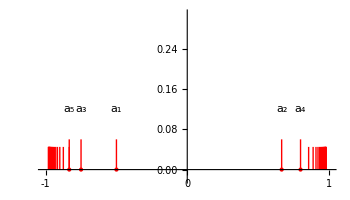

```mathematica
SequenceLinearPlot[Table[(-1)^n n/(n+1),{n,50}],{x,-1.01,1.01},{1,2,3,4,5},0.12,0.06,0.3,Ticks->{{-1,0,1},{}}]
```

Now, we plot the two types of graphs for Example 1 side by side as follows.

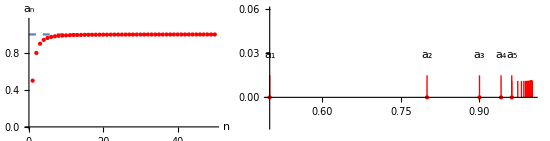

```mathematica
seq=Table[n^2/(n^2+1),{n,1,50}];
GraphicsRow[{
ListPlotWithLimits[seq,{x,0,50},{y,0,1.15},{1}],
SequenceLinearPlot[seq,{x,0.5,1},{1,2,3,4,5},0.029,0.015,0.05]
},Spacings->0,ImageSize->550]
```

Both graphs indicate that the sequence converges to 1. Taking the limit confirms the graph.

```mathematica
Limit[n^2/(n^2+1),n->∞]
```

1

Example 2
Refer to Example 1. How about if a_n=n^2/(n^2+1),n=0,1,2,⋯, i.e., the index starts from 0 rather than 1? 

The first usage of ListPlot does not work. We will have to follow the third usage.

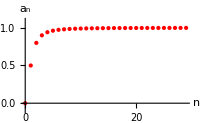

```mathematica
points=Table[{n,n^2/(n^2+1)},{n,0,29}];
ListPlot[points,PlotRange->{-0.1,1.1},PlotStyle->{Red,PointSize[Medium]},AxesLabel->{n,Subscript[a, n]},ImageSize->200]
```

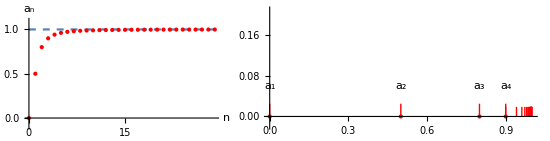

```mathematica
points=Table[{n,n^2/(n^2+1)},{n,0,29}];
GraphicsRow[{
ListPlotWithLimits[points,{x,0,29},{y,-0.1,1.1},{1}],
SequenceLinearPlot[points[[;;,2]],{x,0,1},{1,2,3,4},0.06,0.025,.2]
},Spacings->0,ImageSize->550]
```

Note: PlotRange→{-0.1,1}, but not {0,1}, is used because we want to have space to display full red dots.

Example 3
Generate and plot the first 50 terms of each of the sequences a_n=(-1)^n n^2/(n^2+1),b_n=(-1)^n 2/(n+1),n=1,2,3,⋯. According to the graph, determine whether the sequences are convergent or not.

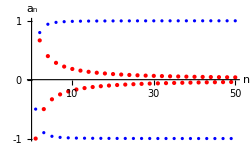

```mathematica
seqs=Table[Table[(-1)^n f,{n,1,50}],{f,{n^2/(n^2+1),2/(n+1)}}];
ListPlot[seqs,ImageSize->250,PlotStyle->{{Blue},{PointSize[Medium],Red}},Ticks->{{10,20,30, 40, 50},{-1,0,1}},AxesLabel->{n,Subscript[a, n]}]
```

Since the values of its terms alternate around 1 or -1 as n is large, the sequence {a_n} is divergent. However, {b_n} converges to 0 from both sides.

## Recursive sequences and cobweb plots

A recursive sequence is a sequence {a_n} of which a_n is expressed in terms of one or more previous terms, such as a_n=a_(n-1)+2,a_1=0,i=2,3,⋯ (or a_(n+1)=a_n+2,a_1=0,i=1,2,⋯). The formula like a_(n+1)=a_n+2 is called a recurrence relation. It is often easy to write out a recurrence relation; but it is not always easy to rewrite the recurrence relation by an explicit formula which directly computes a_n without having to calculate a_(n-1),a_(n-2),⋯, first. For example, the explicit formula for a_(n+1)=a_n+2,a_1=0,i=1,2,⋯, is a_n=2(n-1),n=1,2,⋯, and that for a_(n+1)=a_n+2,a_1=1,i=1,2,⋯, is a_n=2n-1,n=1,2,⋯

NestList is the basic and typical Mathematica built-in function for generating recursive sequences with recurrence relation a_(n+1)=f(a_n).

Recall that in NestList[f,x_1,n], x and f(x) denote the value of the present term and that of the next term of a sequence, respectively; x_1 is the value of the first term of a sequence; and n specifies how many times f(x) is applied to x_1.

Example 4
Generate and plot the first 20 terms of the sequence a_(n+1)=1-a_n^2,a_1=-1,n=1,2,3,⋯.

```mathematica
f[x_]:=1-x^2;
NestList[f,-1,20]
```

{-1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1}

We may also use a pure function (See Unit 2) like

```mathematica
NestList[1-#^2&,-1,20]
```

{-1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1}

The sequence eventually alternates between 1 and 0 and is thus divergent.

Example 5
Generate and plot the first 40 terms of the sequence a_(n+1)=cos a_n,a_1=1,n=1,2,3,⋯.

```mathematica
NestList[Cos[#]&,1.,40] (* 1. can't be 1 here *)
```

{1.,0.540302,0.857553,0.65429,0.79348,0.701369,0.76396,0.722102,0.750418,0.731404,0.744237,0.735605,0.741425,0.737507,0.740147,0.738369,0.739567,0.73876,0.739304,0.738938,0.739184,0.739018,0.73913,0.739055,0.739106,0.739071,0.739094,0.739079,0.739089,0.739082,0.739087,0.739084,0.739086,0.739085,0.739086,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085}

The fixed point of a function and cobweb plots

In Examples 4 and 5, we have seen two recursive sequences of which one is divergent and the other is convergent. Is there any graphical tool which can tell the convergence of a recursive sequence? The cobweb plot is the answer.

If a recursive sequence a_(n+1)=f(a_n), a_1=k,n=1,2,⋯, where k is a constant, is convergent, then, lim_(n→∞) a_n exists and, thus,

lim_(n→∞) a_(n+1)=lim_(n→∞) a_n=L,
L=lim_(n→∞) a_(n+1)=lim_(n→∞) f(a_n)=f(lim_(n→∞) a_n)=f(L).

Now, we not only know the sequence is convergent but also are able to find its limit by solving L=f(L) for L. For example, if we know the sequence a_(n+1)=3+1/2 a_n converges, then we know it converges to

```mathematica
L/.Solve[L==3+1/2 L,L][[1]]
```

6

Here, L is called a fixed point of f(x) for it satisfies the equation x=f(x) which is equivalent to a system of two equations, {y=f(x)
x=y. The cobweb plot may help tell if a fixed point is stable or unstable for a function y=f(x) starting from an initial value x=x_1. For more information, visit https://en.wikipedia.org/wiki/Cobweb_plot.

CobwebPlot

Usage:
                   func: the function f(x) as in x=f(x)
{x,xMin,xMax}: the range of x appears on the graph
                      x_1: the initial value of x
              nCount: how many times f(x) will be called
              arrowq: True - draw arrows on cobweb lines; False - do not draw arrows
       plotOptions: options for Plot

```mathematica
CobwebPlot[func_,{x_,xMin_,xMax_},x1_,nCount_,arrowq_,plotOptions___]:=Module[{f,seq, line},
f[X_]=func/.x->X;
seq=NestList[f,x1,nCount];
line[aug_] = If[arrowq, Arrow[aug], Line[aug]];
Show[{
(* plot f(x) and the axis y = x *)
Plot[{f[x],x},{x,xMin,xMax},plotOptions,PlotStyle->{{Thickness[0.01],Blue},{Dashed,Gray}},ImageSize->260,AspectRatio->Automatic],

(* plot the 1st vertical line segment *)
Graphics[{Red,line[{{x1,0},{x1,seq[[2]]}}]}],
Graphics[{Red,PointSize[Large],Point[{x1,0}]}],
Graphics[{Red,PointSize[Medium],Point[{x1,seq[[2]]}]}],

(* plot other pairs of 2 line segments *)
Table[
Show[{
(* each pair starts at a point on f(x) and ends at a new point on f(x) *)
(* 1. start at (x, f(x)) and end at (f(x), f(x)) on x = y; horizontal *)
Graphics[{Red,line[{{seq[[i]],seq[[i+1]]}, {seq[[i+1]],seq[[i+1]]}}]}],

(* 2. back to (f(x), f(f(x))); vertical *)
Graphics[{Red, line[{{seq[[i+1]],seq[[i+1]]},{seq[[i+1]],seq[[i+2]]}}]}],

Graphics[{Red,PointSize[Medium],Point[{seq[[i+1]],seq[[i+2]]}]}] 
}],{i,1,nCount-2}]
}]]
```

Use CobwebPlot to draw the cobweb plot of  x=f(x)=1-x^2.

```mathematica
NSolve[x==1-x^2,x]
```

{{x→-1.61803},{x→0.618034}}

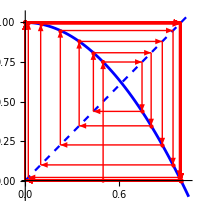

```mathematica
Clear[x]
Module[{x1=.5,nCount=50},
GraphicsRow[{
CobwebPlot[1-x^2,{x,0,1.05},x1,nCount,True,
PlotStyle->{{Blue,Thickness[0.01]},{Dashed,Blue}},ImageSize->200]
}]]
```

There is an outward spiral in this cobweb plot, which indicates the sequence, defined by a_(n+1)=1-a_n^2,a_1=0.5, is divergent, or the fixed point of  1-x^2 is unstable starting from x=0.5.

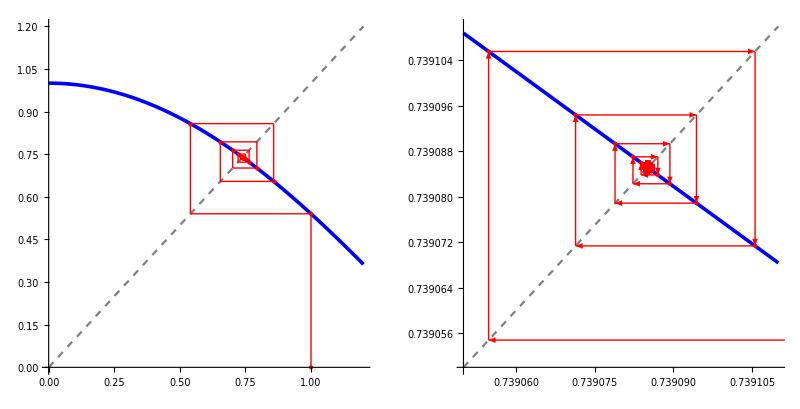

```mathematica
GraphicsRow[{
CobwebPlot[Cos[x],{x,0,1.2},1.,50, False],
CobwebPlot[Cos[x],{x,0.73905,0.73911},1.,50, True] (* zoom in *)
},Spacings->20]
```

There is an inward spiral in the cobweb plot, which says the sequence, defined by a_(n+1)=cos a_n,a_1=1, converges to the fixed point.

```mathematica
x/.NSolve[x==Cos[x],x,Reals][[1]]
```

0.739085

We can use CobwebPlot to make an animation with some changes.

```mathematica
Animate[
CobwebPlot[1-x^2,{x,0,1.05},.5,n,True, PlotStyle->{{Blue,Thickness[0.01]},{Dashed,Blue}}],{n,1,30,1},DefaultDuration->20,AnimationRunning->False]
```

Example 6
Use CobwebPlot to determine if a_(n+1)=1-4(a_n-1/2)^2,n=1,2,⋯, is convergent with a_1=0,1/2,3/4, and 0.45, respectively.

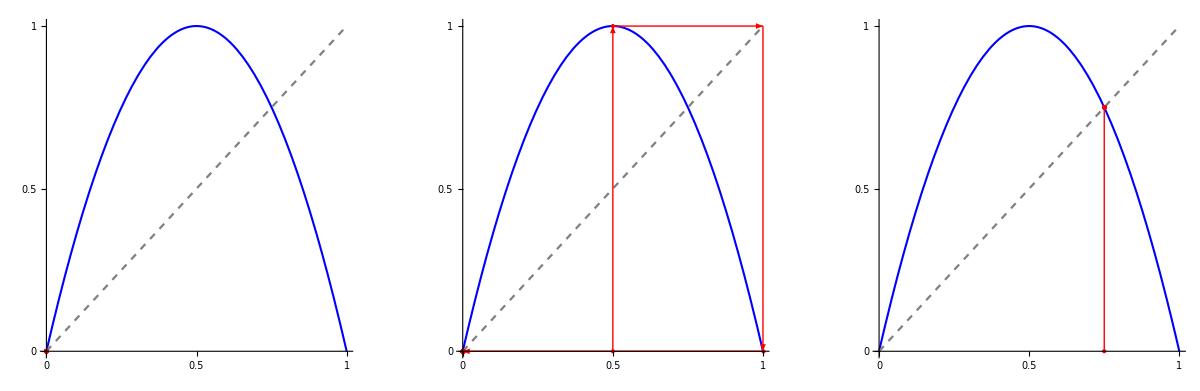

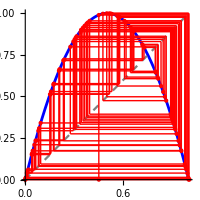

```mathematica
GraphicsRow[{
CobwebPlot[1-4(x-.5)^2,{x,0,1},0,100,False,ImageSize->150,Ticks->{{0,.5,1},{0,.5,1}}],
CobwebPlot[1-4(x-.5)^2,{x,0,1},.5,100,True,ImageSize->150,Ticks->{{0,.5,1},{0,.5,1}}],
CobwebPlot[1-4(x-.5)^2,{x,0,1},.75,100,False,ImageSize->150,Ticks->{{0,.5,1},{0,.5,1}}]
},Spacings->20]
CobwebPlot[1-4(x-.5)^2,{x,0,1},.45,100,False,ImageSize->200]
```

We notice that x=1/2 corresponds to the vertex of the parabola f(x)=1-4(x-1/2)^2, and x = 0 and 3/4 are the two fixed points of f(x) since

```mathematica
x/.Solve[1-4(x-1/2)^2==x,x]
```

{0,3/4}

The three graphs on the top for a_1=0,1/2 and 3/4 show a quick convergence to 0,0, and 3/4, respectively. But the one on the bottom shows the cobweb lines seem to bump randomly and, obviously, the corresponding sequence is divergent, which is true theoretically for any initial value a_1 other than 0,1/2 or 3/4. The following calculations seem to confirm all these.

```mathematica
NestList[1-4(#-.5)^2&,0,10]
```

{0,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
NestList[1-4(#-.5)^2&,.5,10]
```

{0.5,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
NestList[1-4(#-.5)^2&,.75,10]
```

{0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75}

```mathematica
NestList[1-4(#-.5)^2&,.001,20]
```

{0.001,0.003996,0.0159201,0.0626667,0.234958,0.719012,0.808135,0.62021,0.942198,0.217844,0.681551,0.868156,0.457844,0.992891,0.0282324,0.109741,0.390793,0.952295,0.181717,0.594783,0.964065}

```mathematica
NestList[1-4(#-.5)^2&,.501,20]
```

{0.501,0.999996,0.0000159999,0.0000639987,0.000255978,0.00102365,0.00409042,0.0162947,0.0641169,0.240024,0.729649,0.789045,0.665812,0.890026,0.391519,0.952928,0.179426,0.58893,0.968366,0.122534,0.430079}

```mathematica
NestList[1-4(#-.5)^2&,.7501,20]
```

{0.7501,0.7498,0.7504,0.7492,0.751598,0.746793,0.756373,0.737092,0.77515,0.69717,0.844496,0.52529,0.997442,0.0102073,0.0404124,0.155117,0.524223,0.997653,0.00936578,0.0371123,0.14294}

By the way, Unit 6 covers Newton’s method for approximating the root of f(x) near an initial point x_1. The formula

x_(i+1)=x_i-(f(x_i))/(f'(x_i)),i=1,2,⋯

defines a recursive sequence {x_1,x_2,x_3,⋯}. Thus, cobweb plot can be used to explore the performance of Newton’s method, too.

More complicated recursive sequences
Fibonacci sequence is one of the most famous sequences. It is defined by a_(n+2)=a_n+a_(n+1),a_1=1,a_2=1,n=1,2,⋯. From the third term a_3 on, each term depends on two, rather than one, previous terms. There are even more complicated recurrence relation, such as a_(n+3)=2 a_n-5 a_(n+1)+3 a_(n+2). 

When the recurrence relation involves more terms, NestList still works, but awkwardly. In the next example, it is used to generate the first 20 terms of Fibonacci sequence.

Example 7
Use NestList to generate the first 20 terms of the Fibonacci sequence.

```mathematica
Module[{n=20,seq},
seq=Table[1,{n}]; (* allocate space for the sequence with Subscript[a, 1] and Subscript[a, 2] initialized *)
NestList[Module[{},seq[[#+2]]=seq[[#]]+seq[[#+1]];#+1]&,1,n-2];
seq
]
```

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765}

Example 8
Generate and plot the first 20 terms of the Fibonacci sequence.

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765}

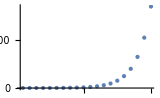

```mathematica
Module[{n=20,seq},
seq=Table[1,{n}];(* allocate space for the sequence with Subscript[a, 1] and Subscript[a, 2] initialized *)
Do[seq[[i+2]]=seq[[i]]+seq[[i+1]],{i,1,n-2}];
Print[seq];
ListPlot[seq,PlotRange->All,PlotStyle->PointSize[Medium],ImageSize->160]
]
```

Fibonacci sequence is so famous and useful that Mathematica provides a built-in function Fibonacci. With the function, the code in Example 8 becomes

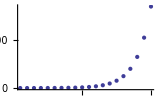

```mathematica
ListPlot[Table[Fibonacci[n],{n,20}],PlotRange->All,PlotStyle->PointSize[Medium],ImageSize->160]
```

That’s nice, isn’t it? However, if a large number of “consecutive” Fibonacci numbers are computed, the built-in function will exhibit very poor performance, which is confirmed by the following computing and comparison. This is one reason why programming is needed in many cases. Mathematica attempts to meet all the needs of all potential users in the world and, thus, provides thousands of built-in functions of which individuals need only a very small number of basic and fundamental functions because they are sufficient if combined with programming capability. In this sense, after some major version such as version 6, all newer versions seem to be the same to many users.

```mathematica
Module[{TimingFibonacciGenerator},
TimingFibonacciGenerator[n_]:=Module[{seq,t},
{n,
Print["Our own code is working on n = ", n, " ..."];
t=Timing[Module[{},seq=Table[1,{n}];Do[seq[[i+2]]=seq[[i]]+seq[[i+1]],{i,1,n-2}]]][[1]];
Print[t, " seconds"],

Print["  Built-in function is working on n = ", n, " ..."];t=Timing[Module[{},seq=Table[Fibonacci[i],{i,n}];  ]][[1]];
Print["  ", t," seconds"]
}];

Join[{
{"n","Seconds used by our own code", "Seconds used by built-in function"}},
Table[TimingFibonacciGenerator[n],{n,{10000,100000,500000}}]
]//TableForm
]
```

Our own code is working on n = 10000 ...

0. seconds

Built-in function is working on n = 10000 ...

0.109375 seconds

Our own code is working on n = 100000 ...

0.1875 seconds

Built-in function is working on n = 100000 ...

4.6875 seconds

Our own code is working on n = 500000 ...

1.85938 seconds

Built-in function is working on n = 500000 ...

Don’t test the built-in function Fibonacci with n=500000 or larger on an ordinary laptop. Otherwise, it will take a long time, and you would possibly have to restart the computer because Evaluation→Quit Kernel→Local or other way may not work.

Example 9
Generate and plot the first 40 terms of the sequence, a_(n+3)=√(-2/5 a_i-2/5 a_(i+1)+8/5 a_(i+2)),a_1=0,a_2=1/2,a_3=1,i=1,2,3,⋯.

```mathematica
seq=Module[{n=40,s},
s=Table[0,{n}]; (* allocate spaces for the sequence with Subscript[a, 1] set to 0 *)
s[[{2,3}]]={0.5,1};
Do[s[[i+3]]=Sqrt[-2/5 s[[i]]-2/5 s[[i+1]]+8/5 s[[i+2]]],{i,1,n-3}];
s
]
```

{0,0.5,1,1.18322,1.13717,0.972717,0.792587,0.651296,0.579614,0.591463,0.673778,0.780778,0.86206,0.893014,0.878457,0.83875,0.795872,0.76584,0.755974,0.76477,0.784159,0.803964,0.81656,0.819297,0.814042,0.805062,0.796721,0.791904,0.791412,0.794235,0.798405,0.80199,0.803821,0.803714,0.802258,0.800374,0.79888,0.79822,0.798405,0.79913}

Now, use ListPlotWithLimits and SequenceLinearPlot to draw the sequence.

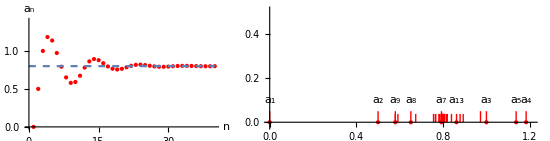

```mathematica
GraphicsRow[{
ListPlotWithLimits[seq,{x,0,40},{y,0,1.4},{0.8}],
SequenceLinearPlot[seq,{x,-0,1.21},{1,2,3,4,5,7,8,9,13},0.1,0.05,0.5]
},Spacings->0,ImageSize->550]
```

CobwebPlot is also applicable to every recursive sequence {a_n} of which the recurrence relation involves multiple previous terms. We assume n is sufficiently large so as to use the plot to approximate the sequence. For example, we take the 10th term of the sequence as the initial value of x_1 and draw the cobweb plot.

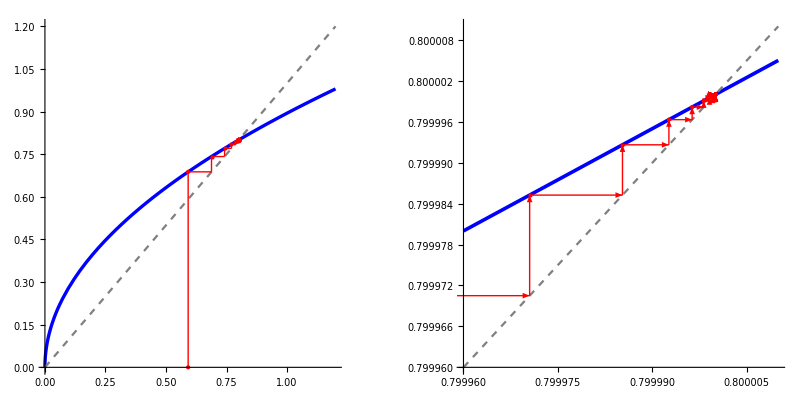

```mathematica
Module[{f},
f[x_]:=Sqrt[-2/5 x-2/5 x+8/5 x];
GraphicsRow[{
CobwebPlot[f[x],{x,0,1.2},seq[[10]],50,False,ImageSize->240],
CobwebPlot[f[x],{x,0.79996,0.80001},seq[[10]],50,True] (* zoom in *)
},Spacings->40]
]
```

A fixed point x^* is say to be attractive or attracting if there is a neighborhood I of x^* such that, for any initial value x_1∈I, x_(n+1)=f(x_n) converges to x^* as n→∞, where x_(n+1)=f(x_n) is a recurrence relation. The plot shows that the fixed point x=0.8 is attractive and the sequence seems to converge to it. We may confirm it by computing

```mathematica
L/.NSolve[L==Sqrt[-2/5 L-2/5 L+8/5 L],L]
```

{0.8,0.}

Is the other fixed point, x=0, also attractive? Try CobwebPlot with any positive x_1 near 0 and see what happens.

Example 10
Generate and plot the first 25 terms of the sequence, a_(n+4)=-a_n+a_(n+3),a_1=0,a_2=1,a_3=1,a_4=0,i=1,2,3,⋯.

{0,1,1,0,0,-1,-2,-2,-2,-1,1,3,5,6,5,2,-3,-9,-14,-16,-13,-4,10,26,39}

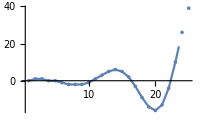

```mathematica
seq=Module[{n=25,s},
s=Table[0,{n}]; (* allocate spaces for the sequence with Subscript[a, 1] and Subscript[a, 4] set to 0 *)
s[[{2,3}]]={1,1};
Do[s[[i+4]]=- s[[i]]+s[[i+3]],{i,1,n-4}];
s
]
Show[{
ListPlot[seq,ImageSize->200,PlotRange->All],
ListPlot[seq,Joined->True]
}]
```

Finding explicit formula for recursive sequences with linear homogeneous recurrence relations

A linear homogeneous recurrence relation of degree k is the recurrence relation of the form

a_n=c_1 a_(n-1)+c_2 a_(n-2)+(⋯c)_k a_(n-k) ⋯⋯⋯⋯⋯⋯⋯⋯⋯ (1)

where c_i,i=1,2,⋯,k, are real constants with c_k≠0.

So, the recurrence relation for the Fibonacci sequence, a_n=a_(n-1)+a_(n-2), is a linear homogeneous recurrence relation of degree 2.

To find an explicit formula of (1), we look for a solution of the form a_n=r^n, and establish the characteristic equation from (1)

r^k-c_1 r^(k-1)-c_2 r^(k-2)-⋯-c_k=0⋯⋯⋯⋯⋯⋯⋯⋯⋯ (2)

If (2) has k distinct roots r_1,r_2,⋯,r_k, then, he explicit formula for the recursive sequence defined by (1) is

a_n=C_1 r_1^n+C_2 r_2^n+⋯+C_k r_k^n

where C_i,i=1,2,⋯,k, are constants which can be determined by applying the initial conditions, a_i,i=1,2,⋯,k.

Similar techniques appear in discrete mathematics, differential equations, and some other courses.

Example 11
Find an explicit formula for the Fibonacci sequences a_n=a_(n-1)+a_(n-2),a_1=1,a_2=1,n=2,3,⋯.

For the recurrence relation is a_n=a_(n-1)+a_(n-2) with c_1=c_2=1, the characteristic equation is r^2-r-1=0.

```mathematica
{r1,r2}=r/.Solve[r^2-r-1==0,r]
```

{1/2 (1-√5),1/2 (1+√5)}

They are two distinct solutions. Therefore, the explicit formula is

```mathematica
f[n_]=c1*r1^n+c2*r2^n;
```

Apply the initial conditions a_1=1 and a_2=1 to find the constants c1 and c2,

```mathematica
cs=Solve[{f[1]==1,f[2]==1},{c1,c2}][[1]]
```

{c1→-((-1+√5) (1+√5))/(4 √5),c2→-(-5-√5)/(5 (1+√5))}

Thus, the explicit formula is

```mathematica
a[n_]=f[n]/.cs//Simplify
```

-(2^-n (5+√5) ((1-√5)^n-(1+√5)^n))/(5 (1+√5))

We can confirm that it works.

```mathematica
Table[a[n],{n,1,20}]//Simplify
```

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765}

Now, we can directly compute, say, the 100th term, without computing terms a_3,a_4,⋯,a_99.

```mathematica
a[100]//Simplify
```

354224848179261915075

## The fixed-point iteration method for solving nonlinear equations

Numerically, we can solve a nonlinear equation f(x)=0 by rewriting it in the form x=g(x) and finding the fixed point of g(x). There are infinitely many choices for g(x), but not each one works. Generated by the iterative formula, x_(n+1)=g(x_n), {x_n} is convergent to the fixed point if |g'(x)|<1 in the neighborhood of that fixed point.

Example 12
Find the root of the equation x e^(0.5x)+1.2x-5=0.

The natural choices of g(x) as in x=g(x) for the equation may be 5/(e^(0.5x)+1.2), (5-x e^(0.5x))/1.2, and (5-1.2x)/ e^(0.5x), and other choices can be x e^(0.5x)+1.2x-5+x, (x e^(0.5x)+1.2x-5+2x)/2, (x e^(0.5x)+1.2x-5+3x)/3, and so on.

Here, we choose g(x)=5/(e^(0.5x)+1.2) and use CobwebPlot to plot the cobweb plot of g(x) starting from x=0.1.

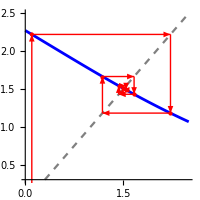

```mathematica
CobwebPlot[5/(E^(0.5x)+1.2),{x,0,2.5},0.1,8,True,
PlotRange->{0.3,2.5},ImageSize->200]
```

The figure shows that there is a fixed point near x=1.5.

If we want to know if |g'(x)|<1 in the neighborhood of the fixed point, we can take the next two steps to determine the range of g'(x) over, say, [0,3].

```mathematica
g[x_]:=5/(E^(0.5x)+1.2)
NSolve[g''[x]==0,x] (* find the critical number(s) of g'(x) *)
```

{{x→0.364643}}

Thus, the absolute extrema of g'(x) over [0,3] can be found.

```mathematica
g'[{0, 3, x/.%[[1]]}]
```

{-0.516529,-0.347078,-0.520833}

Thus,  |g'(x)|<1 over [0,3], which means, starting at any point on [0,3], {x_n} generated by x_(n+1)=g(x_n) always converges to the fixed point of g(x), i.e., the solution to x e^(0.5x)+1.2x-5=0.

```mathematica
NestList[g,0.1,20]
```

{0.1,2.22097,1.18041,1.66425,1.42931,1.54155,1.48746,1.51343,1.50093,1.50694,1.50405,1.50544,1.50477,1.50509,1.50494,1.50501,1.50498,1.50499,1.50499,1.50499,1.50499}

We can verify that x=1.50499 is a numerical solution to x e^(0.5x)+1.2x-5=0.

```mathematica
x E^(0.5x)+1.2x-5/.x->Last[%]
```

-3.03584×10^-6

## Series

A series is the sum of all terms in a sequence. A finite series is ∑_(n=1)^N a_n, where integer N≥1. An infinite series is ∑_(n=1)^∞ a_n. We are usually interested in infinite series. To exam the convergence of an infinite series, we exam the sequence of its partial sums {S_n=∑_(i=1)^n a_i|n=1,2,⋯}. 

The Mathematica built-in functions Sum and NSum have exactly the same usage as Table. Like the difference between Solve and NSolve, in computing ∑expr, Sum gives an exact value while NSum finds a numerical approximation.

```mathematica
Sum[1/n,{n,1,100}]//N
```

5.18738

The following table lists some partial sums of the p-series ∑_(n=1)^∞ 1/n^2, where p=2>1.

```mathematica
Grid[Partition[Table[StringJoin[ToString[Subscript[S,n],FormatType->StandardForm],"=",ToString[NSum[1/i^2,{i,1,n}]]],{n,10000,50000,1000}],5],Frame->All]
```

S_10000=1.64483 | S_11000=1.64484 | S_12000=1.64485 | S_13000=1.64486 | S_14000=1.64486
S_15000=1.64487 | S_16000=1.64487 | S_17000=1.64488 | S_18000=1.64488 | S_19000=1.64488
S_20000=1.64488 | S_21000=1.64489 | S_22000=1.64489 | S_23000=1.64489 | S_24000=1.64489
S_25000=1.64489 | S_26000=1.6449 | S_27000=1.6449 | S_28000=1.6449 | S_29000=1.6449
S_30000=1.6449 | S_31000=1.6449 | S_32000=1.6449 | S_33000=1.6449 | S_34000=1.6449
S_35000=1.64491 | S_36000=1.64491 | S_37000=1.64491 | S_38000=1.64491 | S_39000=1.64491
S_40000=1.64491 | S_41000=1.64491 | S_42000=1.64491 | S_43000=1.64491 | S_44000=1.64491
S_45000=1.64491 | S_46000=1.64491 | S_47000=1.64491 | S_48000=1.64491 | S_49000=1.64491

Numerically, we can tell that these partial sums increase very slowly as n increases. As we already know in Calculus II, the infinite series is convergent and the sum is

```mathematica
Sum[1/n^2,{n,1,∞}]
```

π^2/6

Now, let us exam the case with the harmonic series ∑_(n=1)^∞ 1/n.

```mathematica
Grid[Partition[Table[StringJoin[ToString[Subscript[S,n],FormatType->StandardForm],"=",ToString[NSum[1/i,{i,1,n}]]],{n,10000,50000,1000}],5],Frame->All]
```

S_10000=9.78761 | S_11000=9.88291 | S_12000=9.96992 | S_13000=10.05 | S_14000=10.1241
S_15000=10.1931 | S_16000=10.2576 | S_17000=10.3182 | S_18000=10.3754 | S_19000=10.4294
S_20000=10.4807 | S_21000=10.5295 | S_22000=10.576 | S_23000=10.6205 | S_24000=10.663
S_25000=10.7039 | S_26000=10.7431 | S_27000=10.7808 | S_28000=10.8172 | S_29000=10.8523
S_30000=10.8862 | S_31000=10.919 | S_32000=10.9507 | S_33000=10.9815 | S_34000=11.0113
S_35000=11.0403 | S_36000=11.0685 | S_37000=11.0959 | S_38000=11.1226 | S_39000=11.1485
S_40000=11.1739 | S_41000=11.1986 | S_42000=11.2227 | S_43000=11.2462 | S_44000=11.2692
S_45000=11.2916 | S_46000=11.3136 | S_47000=11.3351 | S_48000=11.3562 | S_49000=11.3768

Again, numerically, we can tell that these partial sums increase very slowly as n increases, but we know the series is (theoretically) divergent! Mathematica also knows.

```mathematica
Sum[1/n,{n,1,∞}]
```

Sum::div: Sum does not converge.

∑_(n=1)^∞ 1/n

That Mathematica is so intelligent is because the capability of symbolic operations as well as rules related to the p-series, the root test, the ratio test, the integral test, etc., have been built into the system.

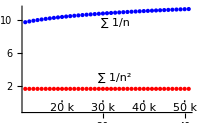

```mathematica
pSums=Table[NSum[1/i^2,{i,1,n}],{n,10000,50000,1000}];
hSums=Table[NSum[1/i,{i,1,n}],{n,10000,50000,1000}];
Show[{
ListPlot[{pSums,hSums},PlotRange->{-1,11.5},Ticks->{{},{2,4,6,8,10}},PlotStyle->{Red,Blue},ImageSize->200],
Graphics[Text["∑ 1/n",{23,9.7}]],
Graphics[Text["∑ 1/n^2",{23,3}]],
Table[{Graphics[Text[(x+10) k,{x,-0.7}]],Graphics[Line[{{x,0},{x,0.25}}]]},{x,10,40,10}]
}]
```

This graph is more useful than the foregoing tables. It seems obviously one series is convergent and the other is unbounded and divergent. But we should be very careful. Numerical computing cannot replace rigorous proof. Please investigate the difference between ∑1/n and ∑1/n^1.0007.

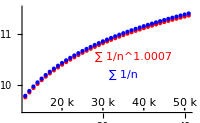

```mathematica
pSums=Table[NSum[1/i^1.0007,{i,1,n}],{n,10000,50000,1000}];
hSums=Table[NSum[1/i,{i,1,n}],{n,10000,50000,1000}];
Show[{
ListPlot[{pSums,hSums},PlotRange->{9.5,11.5},Ticks->{{},{10,11}},PlotStyle->{Red,Blue},ImageSize->200],
Graphics[Text[Style["∑ 1/n^1.0007",Red],{27.6,10.55}]],
Graphics[Text[Style["∑ 1/n",Blue],{25,10.2}]],
Table[{Graphics[Text[(x+10) k,{x,9.65}]],Graphics[Line[{{x,9.5},{x,9.55}}]]},{x,10,40,10}]
}]
```

For n∈[10000,50000], the partial sums S_n=∑_(i=1)^n 1/n and T_n=∑_(i=1)^n 1/n^1.0007are almost coincide. But the latter is convergent since p=1.0007>1.
Note: Here 1.0007 is chosen so as to show the existence of minor difference on the graph. If, say, 1.0000000000000000001, is used, we can hardly discover any difference on the graph or numerically.

## Taylor series

The big-O notation
The big-O notation, e.g., O(n^3), O(n log_2 n), O(h), O(h^2), is commonly used for measuring the magnitude of function values.
Let f(x) and g(x) be two functions defined on some subset of the real numbers.
1. In the case that x→∞: f(x)=O(g(x)) if  there are K>0 and x_0>0 such that, if x>x_0, |f(x)|≤ K|g(x)|.
2. In the case that x→constant a: f(x)=O(g(x)) if  there are K>0 and δ>0 such that, if |x-a|<δ, |f(x)|≤ K|g(x)|.
K, x_0, and δ are witnesses to the relationship f(x)=O(g(x)). The reference function g(x) is not unique. We choose g(x) as “small” (or “large”) as possible when x→∞ (or x→a).

Taylor series
According to Taylor’s Theorem, if f(x) has all continuous derivatives on an open interval I that contains the point x=a, then for every x∈I,

f(x)=f(a)+f'(a)(x-a)+(f''(a))/(2!)(x-a)^2+(f'''(a))/(3!)(x-a)^3+⋯=∑_(k=0)^∞ (f^(k)(a))/(k!)(x-a)^k with f^(0)(a)=f(a)

which is an infinite series, called the Taylor series expansion of f(x) about x=a.

Let P_n(x) be the nth-degree Taylor polynomial of f(x) at x=a, i.e.,

P_n(x)=f(a)+f'(a)(x-a)+(f''(a))/(2!)(x-a)^2+(f'''(a))/(3!)(x-a)^3+⋯+(f^(n)(a))/(n!)(x-a)^n=∑_(k=0)^n (f^(k)(a))/(k!)(x-a)^k.

In Unit 6, P_n(x) is used to approximate f(x) near x=a. We have seen that a larger n gives a better approximation.

Taylor’s Theorem also states that

f(x)=∑_(k=0)^∞ (f^(k)(a))/(k!)(x-a)^k=∑_(k=0)^n (f^(k)(a))/(k!)(x-a)^k+∑_(k=n+1)^∞ (f^(k)(a))/(k!)(x-a)^k=P_n(x)+R_n(x)

where R_n(x)=∑_(k=n+1)^∞ (f^(k)(a))/(k!)(x-a)^k is the remainder with |R_n(x)|≤M/((n+1)!) (|x-a|)^(n+1), if |f^(n+1)(x)|≤M, i.e., R_n(x)=O((x-a)^(n+1)). R_n(x) is also called the truncation error when P_n(x) is used to approximate f(x).

Taylor series expansions play a very important role in numerical computing, especially in the theoretical analysis of algorithms and schemes.

```mathematica
(* generating the nth-degree Taylor polynomial of func(x)at x=x0 *)
TaylorPolynomial[func_,x0_,n_]:=Module[{f},
f[X_]=func/.x->X;
f[x0]+Sum[(D[f[x],{x,i}]/.x->x0)(x-x0)^i/i!,{i,1,n}]
]
```

```mathematica
TaylorPolynomial[Exp[x],0,7]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040

Mathematica provides a built-in function, Series. It does the same job as TaylorPolynomial except that it includes the remainder in the big-O notation. It can also do Taylor series expansion of multivariable functions.

Usage:
Series[f,{x,x_0,n}], generating a power series expansion for f(x) about x=x_0 to order n.

Series[f,{x,x_0,n_x},{y,y_0,n_y},…], generating successively series expansions with respect to x about x=x_0, then y about y=y_0, etc.

```mathematica
Series[Exp[x],{x,0,7}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+O[x]^8

```mathematica
Series[Exp[x+y],{x,0,2},{y,0,3}] (* ⅇ^(x+y)*)
```

(1+y+y^2/2+y^3/6+O[y]^4)+(1+y+y^2/2+y^3/6+O[y]^4) x+(1/2+y/2+y^2/4+y^3/12+O[y]^4) x^2+O[x]^3

Now, let us find Taylor polynomials of various degrees for sin x at x=0 and examine how they approximate the function near x=0.

```mathematica
Clear[x]
Manipulate[
Module[{f,taylorPolynomial, x0},
f[x_]=Sin[x];
x0 = 0;
taylorPolynomial =f[x0]+Sum[(D[f[x],{x,k}]/.x->x0)(x-x0)^k/k!,{k,1,n}];
Show[{
Plot[f[x],{x,-2π,2π},PlotRange->{-1.5,3},PlotStyle->Thickness[0.005],Ticks->{{-2π,-π,0,π,2π},{-1,1}},Axes->{True,False},AspectRatio->Automatic,ImageSize->450],

Plot[taylorPolynomial,{x,-2π,2π},PlotStyle->{Red,Thickness[0.005]}],
Graphics[{Red,Text[StringJoin[ToString[Subscript[P,n],FormatType->StandardForm],"(x) = ",ToString[taylorPolynomial,FormatType->StandardForm]],{0,2.0}]}]
}]],{n,1,17,1}]
```

## Taylor series and finite difference formulas

Assume that there are evenly spaced data points, …,x_(i-2),x_(i-1),x_i,x_(i+1),x_(i+2),…, with h=x_(i+1)-x_i, and f(x_i)=y_i is available at each x_i. If f(x) is not available or f'(x) is hard to evaluate, how to find f'(x_i) numerically? Recall that the Taylor series expansion of f(x) at a is

f(x)=∑_(k=0)^n (f^(k)(a))/(k!)(x-a)^k+O((x-a)^(n+1)).

So, the Taylor series expansion of f(x) at x_i is

f(x)=∑_(k=0)^n (f^(k)(x_i))/(k!)(x-x_i)^k+O((x-x_i)^(n+1)).

Thus, f(x_(i+1))=∑_(k=0)^n (f^(k)(x_i))/(k!)(x_(i+1)-x_i)^k+O((x_(i+1)-x_i)^(n+1)), i.e.,

f(x_(i+1))=f(x_i+h)=∑_(k=0)^n (f^(k)(x_i))/(k!)h^k+O(h^(n+1))=f(x_i)+f'(x_i)h+(f''(x_i))/(2!)h^2+(f'''(x_i))/(3!)h^3+…+(f^(n)(x_i))/(n!)h^n+O(h^(n+1)).

This formula can be used to evaluate f(x_(i+k))=f(x_i+k h), k=…,-2,-1,0,1,2,…, by replacing h with k h in the formula.

```mathematica
(* calculating "coefficients" of the first n+1 terms of the Taylor series expansion of f(Subscript[x, i+j]) at Subscript[x, i] *)
Clear[h]
TaylorCoefs[j_,n_]:=Table[1/k! (j*h)^k, {k,0,n}]
```

```mathematica
TaylorCoefs[-2,5]  (* f(Subscript[x, i-2]) *)
```

{1,-2 h,2 h^2,-(4 h^3)/3,(2 h^4)/3,-(4 h^5)/15}

```mathematica
TaylorCoefs[-1,5]  (* f(Subscript[x, i-1]) *)
```

{1,-h,h^2/2,-h^3/6,h^4/24,-h^5/120}

```mathematica
TaylorCoefs[1,5]  (* f(Subscript[x, i+1]) *)
```

{1,h,h^2/2,h^3/6,h^4/24,h^5/120}

```mathematica
TaylorCoefs[2,5]  (* f(Subscript[x, i+2]) *)
```

{1,2 h,2 h^2,(4 h^3)/3,(2 h^4)/3,(4 h^5)/15}

Thus, we have

f(x_(i-2))=f(x_i)-2f'(x_i)h+2f''(x_i)h^2-4/3 f'''(x_i)h^3+2/3 f^(4)(x_i)h^4-4/15 f^(5)(x_i)h^5+O(h^6)
f(x_(i-1))=f(x_i)-f'(x_i)h+1/2 f''(x_i)h^2-1/6 f'''(x_i)h^3+1/24 f^(4)(x_i)h^4-1/120 f^(5)(x_i)h^5+O(h^6)
f(x_(i+1))=f(x_i)+f'(x_i)h+1/2 f''(x_i)h^2+1/6 f'''(x_i)h^3+1/24 f^(4)(x_i)h^4+1/120 f^(5)(x_i)h^5+O(h^6)
f(x_(i+2))=f(x_i)+2f'(x_i)h+2f''(x_i)h^2+4/3 f'''(x_i)h^3+2/3 f^(4)(x_i)h^4+4/15 f^(5)(x_i)h^5+O(h^6)

To derive a finite difference formula for f'(x_i) using these Taylor series expansions, we multiple them each side by A,B,C,D, respectively, and find their sum so that we can hopefully eliminate terms containing f''(x_i), f'''(x_i), f^(4)(x_i) and obtain

A f(x_(i-2))+B f(x_(i-1))+C f(x_(i+1))+D f(x_(i+2))=K f(x_i)+M f'(x_i)h+O(h^5)

which gives the formula

f'(x_i)=[A f(x_(i-2))+B f(x_(i-1))-K f(x_i)+C f(x_(i+1))+D f(x_(i+2))]/(M h)+O(h^4).

The following code finds the coefficients A,B,K,C,D, and M.

```mathematica
coefs=Solve[{
2A+1/2 B+1/2 C+2D==0,(* eliminate f'' *)
-4/3 A-1/6 B+1/6 C+4/3 D==0,(* eliminate f''' *)
2/3 A+1/24 B+1/24 C+2/3 D==0,(* eliminate f'''' *)
A==1 (* chose any none-zero number and always obtain parallel solutions {A, B, C, D, K, M} *)
},{A,B,C,D}][[1]]
```

{A→1,B→-8,C→8,D→-1}

```mathematica
{K,M}={A+B+C+D,-2A-B+C+2D}/. coefs
```

{0,12}

Therefore, we obtain the four-point central finite difference formula

f'(x_i)=[f(x_(i-2))-8 f(x_(i-1))+8 f(x_(i+1))- f(x_(i+2))]/(12h)+O(h^4).

This idea can help us find all other finite difference formulas for f'(x_i),f''(x_i),f'''(x_i),… For example, the following code

```mathematica
coefs=Solve[{
-2 A-B+C+2 D==0,(* eliminate f' *)
-4/3 A-1/6 B+1/6 C+4/3 D==0,(* eliminate f''' *)
2/3 A+1/24 B+1/24 C+2/3 D==0,(* eliminate f'''' *)
-4/15 A-1/120 B+1/120 C+4/15 D==0,(* eliminate f''''' *)
A==-1 (* The 4 eqs above are linearly dependent. Assign any nonzero number to A. *)
},{A,B,C,D}][[1]]
```

{A→-1,B→16,C→16,D→-1}

```mathematica
{K,M}={A+B+C+D,2 A+1/2 B+1/2 C+2 D}/. coefs
```

{30,12}

generates the five-point central finite difference formula

f''(x_i)=[-f(x_(i-2))+16 f(x_(i-1))-30 f(x_i)+16 f(x_(i+1))- f(x_(i+2))]/(12 h^2)+O(h^4).

The Julia and Python packages
Applying a similar but more general approach, the open source Julia and Python packages, found at https://github.com/fdformula/, are each a comprehensive toolkit for generating forward, backward, and central finite difference formulas, working with Taylor series expansions, and so on. Both work independently. They can also determine if there is a formula for a derivative that uses any given points, e.g., x_(i-2),x_i,x_(i+1),x_(i+5),x_(i+6),x_(i+15). If it exists, they can each generate the formula.

© 2015-2024 by David Wang, dwang@liberty.edu